# DIFFERENTIAL EQUATION PRACTICAL

## Name: Om Gupta Roll No.:

#### 1. Solve the following differential equation and find the general solution : y'' + 5 y' - 6 y = 0

```mathematica
eqn1 = y''[x]+5y'[x]-6y[x]==0;
```

```mathematica
sol1 = DSolve[eqn1,y,x]
```

{{y→Function[{x},ⅇ^(-6 x) C[1]+ⅇ^x C[2]]}}

#### 2. Solve the following initial value problem y’’-2y’+y=0, y(0)=1, y’(0)=-1 Plot the solution also

```mathematica
eqn2 = y''[x]-2y'[x]+y[x]==0;
```

```mathematica
sol2 = DSolve[{eqn2, y[0]==1, y'[0]==-1}, y, x]
```

{{y→Function[{x},-ⅇ^x (-1+2 x)]}}

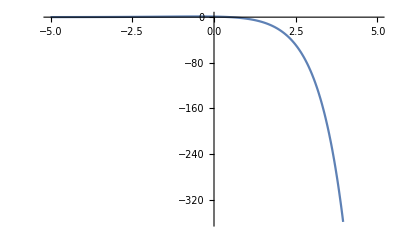

```mathematica
Plot[y[x]/.sol2, {x,-5,5}]
```

#### 3. Solve the following non-homogenous ODE using methods of variation of parameters y''-2y'+y=e^xsinx

```mathematica
eqn3 = y''[x]-2y'[x]+y[x]==Exp[x]*Sin[x];
```

```mathematica
sol3 = DSolve[eqn3,y,x]
```

{{y→Function[{x},ⅇ^x C[1]+ⅇ^x x C[2]-ⅇ^x Sin[x]]}}

#### 4. Find the solution of the following Cauchy problem 3 u_x+2 u_y=0, u(x,0)=sinx

```mathematica
eqn4 = 3D[u[x,y],x]+2D[u[x,y],y]==0;
```

```mathematica
sol4 = DSolve[{eqn4, u[x,0]==Sin[x]},u[x,y],{x,y}]
```

{{u[x,y]→-Sin[3/2 (-(2 x)/3+y)]}}

#### 5. Find the general solution and plot the following PDE using plot label xu_x+yu_y=u

```mathematica
eqn5 = x D[u[x,y],x]+y D[u[x,y],y]==u[x,y];
```

```mathematica
sol5 = DSolve[eqn5,u[x,y],{x,y}]
```

{{u[x,y]→x C[1][y/x]}}

```mathematica
Plot3D[u[x,y]/.sol5/.C[1][y/x]->y/x,{x,-10,10},{y,-10,10}]
```

-Graphics3D-